```mathematica
sol0=DSolve[{g'[t]==-1/tC g[t],
g[0]==g0},g[t],t]
```

{{g[t]→ⅇ^(-t/tC) g0}}

```mathematica
sol1=DSolve[{
g'[t]==-1/tC g[t]+gR[t],
gR'[t]==-1/tCR gR[t],
gR[0]==gR0,
g[0]==g0
},{g[t],gR[t]},t]
```

{{g[t]→-1/(tC-tCR)ⅇ^(-t/tC-t/tCR) (-ⅇ^(t/tCR) g0 tC+ⅇ^(t/tCR) g0 tCR+ⅇ^(t/tC) gR0 tC tCR-ⅇ^(t/tCR) gR0 tC tCR),gR[t]→ⅇ^(-t/tCR) gR0}}

```mathematica
Simplify[(g[t]/.sol1[[1]])==1/(tC-tCR)(ⅇ^(-t/tC) (tC-tCR) g0+(ⅇ^(-t/tC)-ⅇ^(-t/tCR)) (gR0 tC tCR))]
```

True

```mathematica
Simplify[(g[t]/.sol1[[1]])==(ⅇ^(-t/tC) g0+(ⅇ^(-t/tC)-ⅇ^(-t/tCR)) (gR0 tC tCR)/(tC-tCR))]
```

True

```mathematica
Simplify[(g[t]/.sol1[[1]])==(ⅇ^(-t/tC) g0+ⅇ^(-t/tCR) (ⅇ^((1/tCR-1/tC) t)-1) gR0/(1/tCR-1/tC))]
```

True

```mathematica
Simplify[(g[t]/.sol1[[1]])==ⅇ^(-t/tC) (g0+gR0 (ⅇ^((1/tC-1/tCR) t)-1)/(1/tC-1/tCR))]
```

True

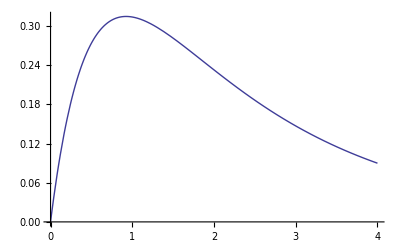

```mathematica
Plot[g[t]/.sol1/.{tC->2,tCR->0.5,g0->0,gR0->1},{t,0,4}]
```

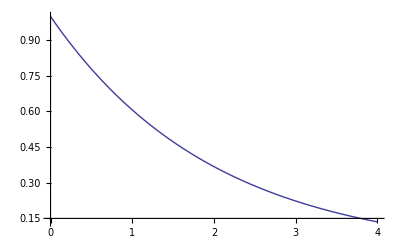

```mathematica
Plot[g[t]/.sol0/.{tC->2,tCR->0.5,g0->1},{t,0,4}]
```

```mathematica
(* Verify *)
```

```mathematica
(* ======= I&F model ======= *)
(* Constants *)
ϵL=0;
Vth=1;
GL=1/20;
ϵE=14/3;
ϵI=-2/3;
σE=2;
σHE=1/2;
σI=5;
σHI=4/5;
```

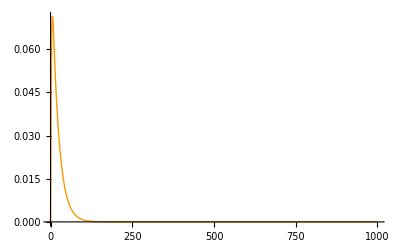

```mathematica
(* Solve V,G,H *)
Tmax=1000; (* ms *)
u0=0;
sGH=NDSolve[{
u'[t]==If[u[t]<Vth,-GL*(u[t]-ϵL)-gE[t] (u[t]-ϵE),0],
gE'[t]==-gE[t]/σE+hE[t],
hE'[t]==-hE[t]/σHE,
hE[0]==0.02,
gE[0]==0,
u[0]==u0
},{u[t],gE[t],hE[t]},{t,0,Tmax}];
(*Plot[Evaluate[u[t]/.s]-u0,{t,0,Tmax},PlotRange->All]*)
g2=Plot[Evaluate[u[t]/.sGH],{t,0,Tmax},PlotRange->All,PlotStyle->{Hue[0.1]}]
```

```mathematica
li1=BinaryReadList["/home/xyy/code/vec_IFsimu/v_volt.dat","Real64"];
lli1=Table[{(i-1)*0.125,li1[[i]]},{i,1,Length[li1]}];
```

```mathematica
gg1=ListPlot[lli1[[1;;100]],PlotRange->All]
```

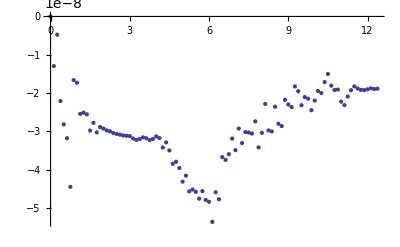

```mathematica
diffli1=Table[{(i-1)*0.125,li1[[i]]-Evaluate[u[t]/.sGH[[1]]/.t->(i-1)*0.125]},{i,1,Length[li1]}];
ListPlot[diffli1[[1;;100]],PlotRange->All]
```